```mathematica
f[n_,r_]:=((1+r^2)^n)/(Sqrt[(n+1)^2+(n r)^2]∏_(m=1)^n Sqrt[(1+((m-1)/m r)^2)*(((m-1)/m)^2+r^2)])
```

```mathematica
ll=Table[{r,f[1000,1.*r]},{r,Join[Table[1.+i/10.,{i,1,20}],Table[i,{i,3,100}]]}]
```

{{1.1,0.849267043529944},{1.2,0.826098347073295},{1.3,0.811960546748724},{1.4,0.804210501014581},{1.5,0.800999706909886},{1.6,0.801013394102003},{1.7,0.803304049705007},{1.8,0.807182123536712},{1.9,0.812142398910611},{2.,0.817813243350739},{2.1,0.823920928064109},{2.2,0.83026411395016},{2.3,0.836695346845245},{2.4,0.843107478128173},{2.5,0.849423603759199},{2.6,0.855589552157858},{2.7,0.861568240419745},{2.8,0.867335413610309},{2.9,0.872876416320831},{3.,0.878183739893984},{3,0.878183739893984},{4,0.919164530359409},{5,0.943831031941268},{6,0.959137818123167},{7,0.969104537086767},{8,0.975893865774102},{9,0.98070187734586},{10,0.984220174675554},{11,0.98686686331941},{12,0.988905137749223},{13,0.990506700092239},{14,0.991787125803762},{15,0.992826374359548},{16,0.993681116074668},{17,0.994392381416152},{18,0.994990445811485},{19,0.995498030310061},{20,0.995932447787157},{21,0.996307072401783},{22,0.996632364872402},{23,0.996916600210388},{24,0.997166392401879},{25,0.997387078146875},{26,0.997583001228193},{27,0.997757725808834},{28,0.997914198219426},{29,0.998054870952784},{30,0.998181798612437},{31,0.998296712827316},{32,0.998401081234349},{33,0.998496154282021},{34,0.998583002643223},{35,0.99866254732762},{36,0.998735584076122},{37,0.998802803244019},{38,0.998864806100451},{39,0.998922118263949},{40,0.998975200833625},{41,0.999024459657087},{42,0.999070253082855},{43,0.999112898473526},{44,0.999152677701142},{45,0.999189841802357},{46,0.999224614936944},{47,0.99925719776611},{48,0.999287770346145},{49,0.999316494614713},{50,0.99934351653426},{51,0.999368967945686},{52,0.99939296817571},{53,0.999415625435067},{54,0.999437038037707},{55,0.999457295467077},{56,0.999476479310498},{57,0.999494664080586},{58,0.999511917938473},{59,0.999528303332325},{60,0.999543877562238},{61,0.999558693281077},{62,0.999572798939424},{63,0.999586239181486},{64,0.999599055198284},{65,0.999611285043241},{66,0.999622963914501},{67,0.999634124408192},{68,0.999644796745809},{69,0.999655008978785},{70,0.999664787172601},{71,0.999674155573394},{72,0.999683136757947},{73,0.999691751769909},{74,0.999700020242794},{75,0.99970796051203},{76,0.999715589716521},{77,0.999722923891103},{78,0.999729978050752},{79,0.999736766267539},{80,0.999743301740656},{81,0.999749596860635},{82,0.999755663268126},{83,0.99976151190762},{84,0.999767153076733},{85,0.999772596471823},{86,0.999777851229249},{87,0.999782925964013},{88,0.999787828804968},{89,0.999792567427278},{90,0.999797149082607},{91,0.999801580626742},{92,0.999805868545284},{93,0.999810018977412},{94,0.999814037737719},{95,0.999817930336748},{96,0.999821701999781},{97,0.999825357684414},{98,0.999828902096751},{99,0.999832339706678},{100,0.999835674761892}}

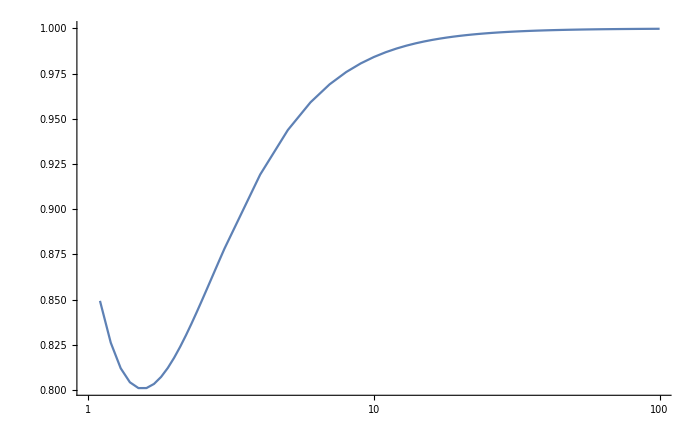

```mathematica
ListLogLinearPlot[ll,PlotRange->All,Joined->True]
```